```mathematica
L[x_,r_]=4 r x(1-x)
Logistic[x0_,n_,r_]:=NestList[L[#,r]&,x0,n]
DF[x_,r_]=D[L[x,r],x]
LYALogistic[list_,r_]:=1/Length[list]  Total[Log[Abs[DF[#,r]]]&/@list]
```

4 r (1-x) x

4 r (1-x)-4 r x

```mathematica
LYALogistic[Logistic[0.3,20,3.5/4.0],3.5/4.0]
DF[#,3.5/4.0]&/@Logistic[0.3,20,3.5/4.0]
```

-0.0380313

{1.4,-1.645,-1.27199,-1.81602,-0.976029,-2.14868,-0.316578,-2.57489,0.690027,-2.38693,0.223721,-2.59997,0.754934,-2.34004,0.112888,-2.61863,0.803607,-2.30211,0.0248509,-2.62469,0.819502}

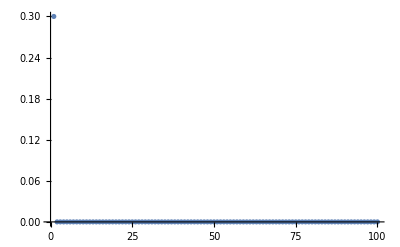
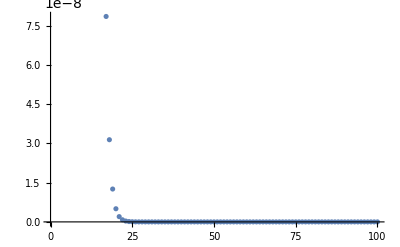
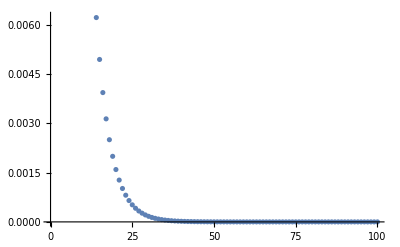
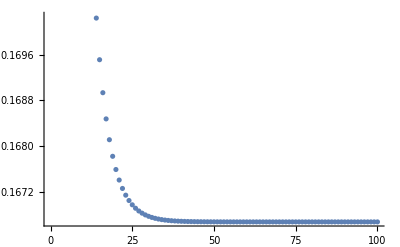
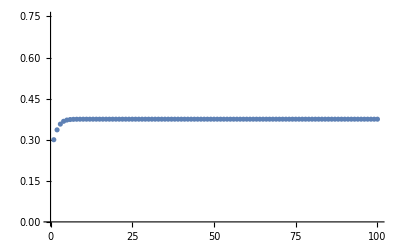
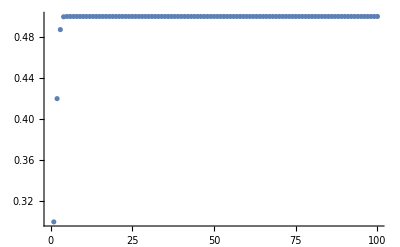
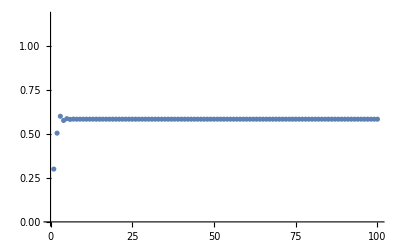
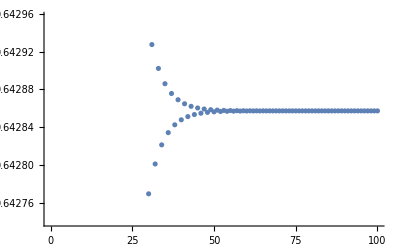

```mathematica
eachDomain=Range[0,1,.1];
points=Logistic[.3, 10000, #]&/@eachDomain;
ListPlot[ #[[1;;100]] ]&/@points
(*Histogram[#]&/@points*)
Histogram[#,{0,1,.05}]&/@points
```

```mathematica
BifurcationDiagram[r1_:0,r2_:1,iterations_:1000,resolution_:1000]:=(Module[{rs},
rs=Range[r1,r2,(r2-r1)/resolution];
ListPlot[
Flatten[
Partition[
Riffle[
Logistic[0.5,iterations,#],
#][[100;;iterations]],
2]&/@rs
,1]
,ImageSize->1000,PlotStyle->{Directive[PointSize[.000000001],Opacity[.05]]}]
])
LyapunovPlot[r1_:0,r2_:1,iterations_:1000]:=Plot[LYALogistic[Logistic[0.3,iterations,r],r],{r,r1,r2},ImageSize->1000,PlotStyle->Red,PlotRange->Full]
```

-Graphics-

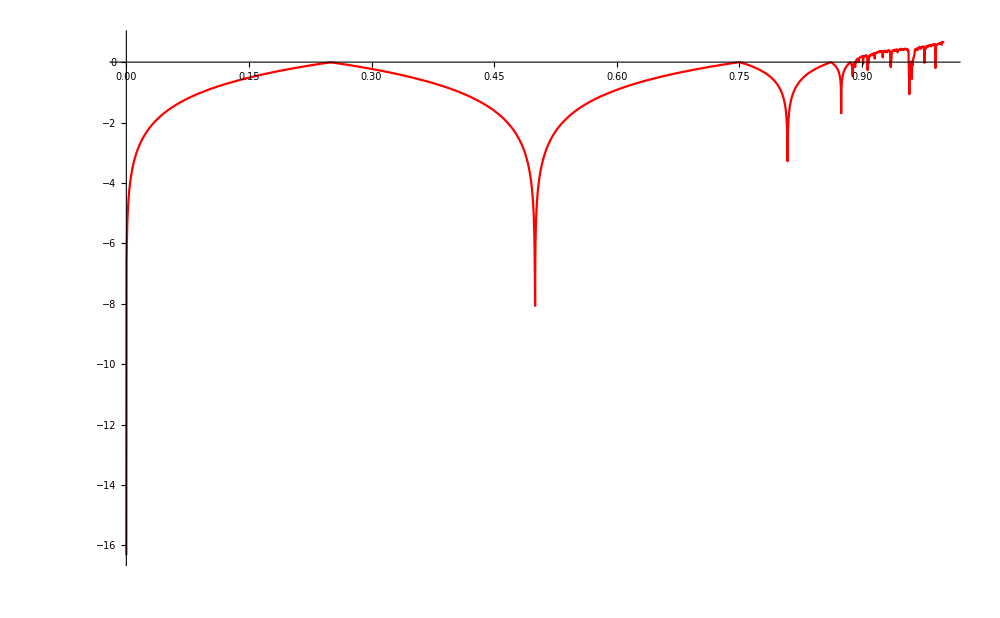

-Graphics-

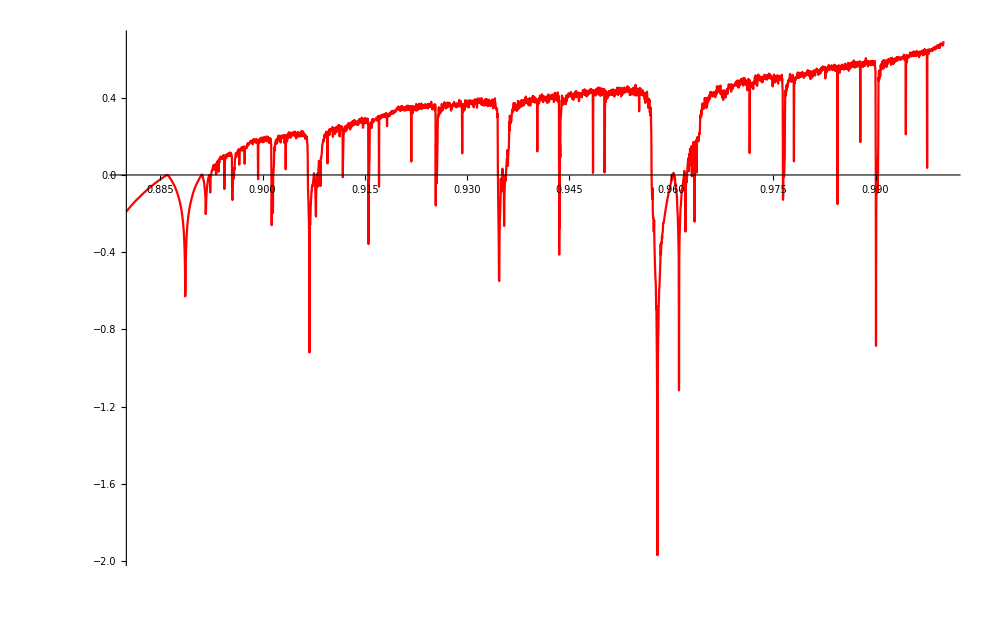

```mathematica
BifurcationDiagram[]
LyapunovPlot[]
BifurcationDiagram[0.88]
LyapunovPlot[.88]
```

```mathematica
p
```

p